```mathematica
(* ====== Liberia ====== *)
ClearAll[n,d,A,M,S,U,p,q,a,x,Udata,Mdata,Adata,Ddata,Sdata];

n=3441790;
Udata = {766,795,824,847,870,892,915,938,949,959,983,1007,1031,1055,1079,1104,1128,1152,1175,1199,1255,1255,1302,1355,1371,1386,1402,1423,1443,1478,1493,1514,1535,1556,1566,1575,1596,1616,1636,1657,1677,1700,1700,1728,1756,1770,1783,1796,1805,1805,1838,1870,1885,1900,1915,1891,1891,1984,1984,2003,2022,2041,2041,2051,2061,2074,2095,2115,2136,2150,2150,2166,2192,2241,2263,2263,2273,2285,2316,2347,2378,2394,2394,2406}
Mdata = {1179,1180,1182,1185,1186,1188,1189,1191,1191,1192,1192,1193,1194,1194,1195,1196,1196,1197,1197,1198,1198,1198,1199,1199,1200,1201,1202,1202,1203,1204,1205,1205,1206,1206,1207,1207,1208,1208,1209,1209,1210,1210,1211,1212,1213,1214,1214,1215,1215,1217,1218,1220,1222,1223,1226,1227,1228,1229,1230,1234,1236,1237,1240,1241,1242,1243,1244,1245,1246,1249,1251,1252,1257,1259,1260,1262,1264,1267,1268,1269,1270,1274,1280,1287}
Adata = {4523,4603,4683,4758,4832,4907,4981,5056,5104,5152,5210,5268,5325,5383,5441,5518,5595,5674,5752,5831,5978,5978,6039,6201,6240,6278,6317,6346,6375,6457,6497,6544,6591,6638,6670,6702,6779,6856,6896,6935,6975,7017,7017,7089,7160,7215,7271,7326,7354,7354,7415,7476,7507,7539,7570,7602,7602,7759,7759,7761,7764,7766,7766,7786,7802,7825,7844,7864,7883,7903,7903,7909,7921,7963,7968,7968,7977,7989,8007,8024,8042,8059,8059,8063}
Ddata = {1169,1178,1187,1200,1212,1225,1237,1250,1259,1267,1293,1319,1346,1372,1398,1431,1463,1485,1508,1530,1583,1583,1609,1660,1687,1715,1742,1755,1768,1857,1899,1944,1988,2033,2059,2085,2281,2477,2503,2530,2556,2582,2582,2619,2655,2681,2706,2732,2758,2758,2793,2827,2856,2886,2915,2943,2943,2977,2977,3001,3025,3049,3049,3062,3067,3083,3099,3116,3132,3145,3145,3153,3159,3195,3199,3199,3207,3216,3235,3255,3274,3276,3276,3286}
Sdata = {6432416,6432297,6432177,6432063,6431953,6431841,6431731,6431618,6431550,6431483,6431375,6431266,6431157,6431049,6430940,6430804,6430671,6430545,6430421,6430295,6430039,6430039,6429904,6429638,6429555,6429473,6429390,6429327,6429264,6429057,6428959,6428846,6428733,6428620,6428551,6428484,6428189,6427896,6427809,6427722,6427635,6427544,6427543,6427405,6427269,6427173,6427079,6426984,6426921,6426919,6426789,6426660,6426583,6426505,6426427,6426390,6426389,6426104,6426103,6426054,6426006,6425960,6425957,6425913,6425881,6425828,6425771,6425713,6425656,6425606,6425604,6425573,6425524,6425395,6425363,6425361,6425332,6425296,6425227,6425158,6425089,6425050,6425044,6425011}
ϵ=Sum[(Udata[[i+1]]-Udata[[i]]+p*Udata[[i]]-x/n*Sdata[[i]]*(Mdata[[i]]+Adata[[i]]))^2,{i,Length@Udata-1}]
N@Minimize[ϵ,{x,p}]
```

{766,795,824,847,870,892,915,938,949,959,983,1007,1031,1055,1079,1104,1128,1152,1175,1199,1255,1255,1302,1355,1371,1386,1402,1423,1443,1478,1493,1514,1535,1556,1566,1575,1596,1616,1636,1657,1677,1700,1700,1728,1756,1770,1783,1796,1805,1805,1838,1870,1885,1900,1915,1891,1891,1984,1984,2003,2022,2041,2041,2051,2061,2074,2095,2115,2136,2150,2150,2166,2192,2241,2263,2263,2273,2285,2316,2347,2378,2394,2394,2406}

{1179,1180,1182,1185,1186,1188,1189,1191,1191,1192,1192,1193,1194,1194,1195,1196,1196,1197,1197,1198,1198,1198,1199,1199,1200,1201,1202,1202,1203,1204,1205,1205,1206,1206,1207,1207,1208,1208,1209,1209,1210,1210,1211,1212,1213,1214,1214,1215,1215,1217,1218,1220,1222,1223,1226,1227,1228,1229,1230,1234,1236,1237,1240,1241,1242,1243,1244,1245,1246,1249,1251,1252,1257,1259,1260,1262,1264,1267,1268,1269,1270,1274,1280,1287}

{17035.3,{x→0.00378024,p→0.0223951}}

```mathematica
p=0.022395099927995137
ϵ=Sum[(Udata[[i+1]]-Udata[[i]]+p*Udata[[i]]-x/n*Sdata[[i]]*(Mdata[[i]]+Adata[[i]]))^2,{i,Length@Udata-1}]
N@Minimize[ϵ,{x}]
```

0.00602125

{42962.3,{x→0.00669021}}

```mathematica
ClearAll[ϵ,q]
q=0.009379024655119134;
ϵ=Sum[(Mdata[[i+1]]-Mdata[[i]]+q*Mdata[[i]]-p*Udata[[i]])^2,{i,Length@Udata-1}]
(*Plot[ϵ[x],{x,-0.0001,0.0001}]*)
(*For[q=0,q<50,q++,Print[ϵ]]*)
N@Minimize[{ϵ},{p}]
```

{3733.45,{p→0.00602125}}

```mathematica
ClearAll[ϵ]
a = 0.00360921;
ϵ=Sum[(Adata[[i+1]]-Adata[[i]]+a*Adata[[i]]-q*Mdata[[i]])^2,{i,Length@Ddata-1}]
N@Minimize[ϵ,{q}]
```

{89075.6,{q→0.0547557}}

```mathematica
ClearAll[ϵ]
ϵ=Sum[(Ddata[[i+1]]-Ddata[[i]]-a*Adata[[i]])^2,{i,Length@Ddata-1}]
N@Minimize[ϵ,{a}]
```

{80634.8,{a→0.00360921}}

0.00378024

0.0223951

0.0547557

0.00360921

6440053

{{S→InterpolatingFunction[{{0.,90.}},<>],U→InterpolatingFunction[{{0.,90.}},<>],M→InterpolatingFunction[{{0.,90.}},<>],A→InterpolatingFunction[{{0.,90.}},<>],d→InterpolatingFunction[{{0.,90.}},<>]}}

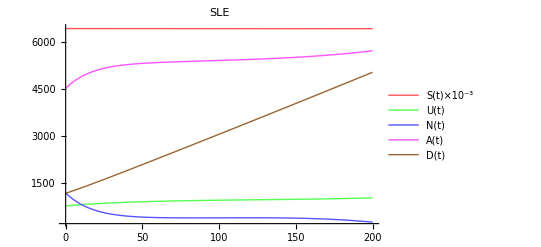

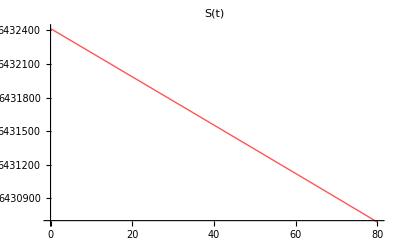

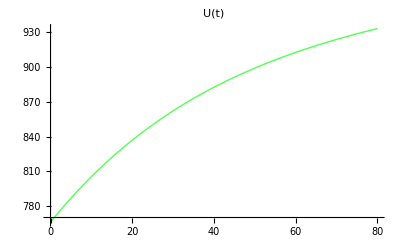

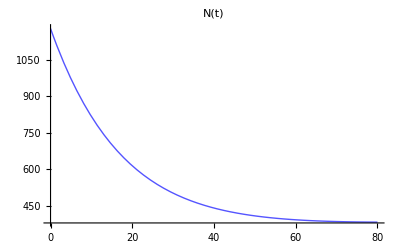

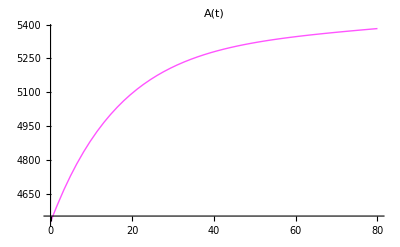

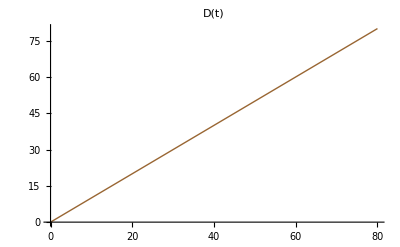

```mathematica
x=0.00378024
p=0.0223951
q=0.0547557
a=0.00360921
n = 6440053
eq= NDSolve[{U'[t]==x/n*S[t]*(M[t]+A[t])-p*U[t],S'[t]==-x/n*S[t]*(M[t]+A[t]),M'[t]==p*U[t]-q*M[t],A'[t]==q*M[t]-a*A[t],d'[t]==a*A[t],U[0]==766,M[0]==1179,A[0]==4523,d[0]==1169,S[0]==6432416},{S,U,M,A,d},{t,0,90}]

SetOptions[Plot,BaseStyle->{FontSize->14}];
(*For[i=0,i<87,i++,Print[N[(U[i]/.eq),1][[1]]]]*)
(*Plot[{(*U[t]/.eq,S[t]/.eq*),M[t]/.eq,(*A[t]/.eq,d[t]/.eq*)},{t,0,469},PlotRange->All]
Plot[{(*U[t]/.eq,S[t]/.eq,M[t]/.eq,*)A[t]/.eq(*,d[t]/.eq*)},{t,0,469},PlotRange->All]
Plot[{(*U[t]/.eq,S[t]/.eq,M[t]/.eq,A[t]/.eq,*)d[t]/.eq},{t,0,86000},PlotRange->All]*)
SetOptions[Plot,BaseStyle->{FontSize->14}];

Plot[{(S[t]/(10^3)/.eq),(U[t]/.eq),(M[t]/.eq),(A[t]/.eq),(d[t]/.eq)},{t,0,200},PlotRange->All,PlotLegends->{"S(t)×10^-3","U(t)","N(t)","A(t)","D(t)"},PlotLabel->"SLE",PlotStyle->{{Lighter[Red],Thick},{Lighter[Green],Thick},{Lighter[Blue],Thick},{Lighter[Magenta],Thick},{Brown,Thick}}]

(*Plot[{(A[t]/.eq),(d[t]/.eq),(M[t]/.eq),(U[t]/.eq)},{t,0,90},PlotRange->All,PlotLegends->{"A(t)", "D(t)", "N(t)","U(t)"}]
Plot[{(*(M[t]/.eq),*)(S[t]/.eq)},{t,0,880},PlotLabel->"SLE",PlotRange->All,PlotLegends->"S(t)"]
Plot[{(M[t]/.eq),(U[t]/.eq)},{t,0,86},PlotRange->All,PlotLegends->{"N(t)","U(t)"}]*)
Plot[{(S[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"S(t)",PlotStyle->{Lighter[Red],Thick}]
Plot[{(U[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"U(t)",PlotStyle->{Lighter[Green],Thick}]
Plot[{(M[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"N(t)",PlotStyle->{Lighter[Blue],Thick}]
Plot[{(A[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"A(t)",PlotStyle->{Lighter[Magenta],Thick}]
Plot[{(D[t]/.eq)},{t,0,80},PlotRange->All,PlotLabel->"D(t)",PlotStyle->{Brown,Thick}]
```

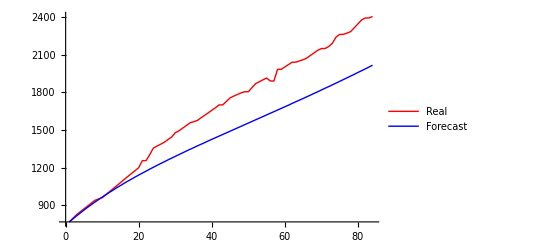

```mathematica
ListLinePlot[{{766,795,824,847,870,892,915,938,949,959,983,1007,1031,1055,1079,1104,1128,1152,1175,1199,1255,1255,1302,1355,1371,1386,1402,1423,1443,1478,1493,1514,1535,1556,1566,1575,1596,1616,1636,1657,1677,1700,1700,1728,1756,1770,1783,1796,1805,1805,1838,1870,1885,1900,1915,1891,1891,1984,1984,2003,2022,2041,2041,2051,2061,2074,2095,2115,2136,2150,2150,2166,2192,2241,2263,2263,2273,2285,2316,2347,2378,2394,2394,2406},{766,790,814,837,860,882,903,924,944,964,983,1002,1020,1039,1056,1074,1091,1107,1124,1140,1156,1171,1187,1202,1217,1232,1246,1261,1275,1289,1303,1317,1331,1345,1358,1372,1385,1398,1412,1425,1438,1451,1464,1477,1490,1503,1516,1529,1542,1555,1568,1581,1594,1607,1620,1633,1646,1659,1672,1685,1698,1712,1725,1738,1751,1765,1778,1792,1805,1819,1833,1846,1860,1874,1888,1902,1916,1930,1944,1959,1973,1987,2002,2017}},PlotStyle->{Red,Blue},PlotLegends->{"Real","Forecast"}]
```

```mathematica
x=0.0116283467251707
p=0.0373465631070888
q=0.271443868230962
a=0.00275654157000076
n = 6440053
eq= NDSolve[{U'[t]==x/n*S[t]*(M[t]+A[t])-p*U[t],S'[t]==-x/n*S[t]*(M[t]+A[t]),M'[t]==p*U[t]-q*M[t],A'[t]==q*M[t]-a*A[t],d'[t]==a*A[t],U[0]==766,M[0]==79,A[0]==4523,d[0]==1169,S[0]==6433516},{S,U,M,A,d},{t,0,90}]
For[i=0,i<85,i++,Print[N[(S[i]/.eq),1][[1]]]]
```

0.0116283

0.0373466

0.271444

0.00275654

6440053

{{S→InterpolatingFunction[{{0.,90.}},<>],U→InterpolatingFunction[{{0.,90.}},<>],M→InterpolatingFunction[{{0.,90.}},<>],A→InterpolatingFunction[{{0.,90.}},<>],d→InterpolatingFunction[{{0.,90.}},<>]}}

```mathematica
forecast = {6.43352*^6,6.43346*^6,6.43341*^6,6.43335*^6,6.4333*^6,6.43325*^6,6.43319*^6,6.43314*^6,6.43308*^6,6.43303*^6,6.43297*^6,6.43291*^6,6.43286*^6,6.4328*^6,6.43274*^6,6.43269*^6,6.43263*^6,6.43257*^6,6.43251*^6,6.43246*^6,6.4324*^6,6.43234*^6,6.43228*^6,6.43222*^6,6.43216*^6,6.4321*^6,6.43204*^6,6.43198*^6,6.43191*^6,6.43185*^6,6.43179*^6,6.43173*^6,6.43166*^6,6.4316*^6,6.43154*^6,6.43147*^6,6.43141*^6,6.43134*^6,6.43128*^6,6.43121*^6,6.43114*^6,6.43108*^6,6.43101*^6,6.43094*^6,6.43087*^6,6.4308*^6,6.43073*^6,6.43066*^6,6.43059*^6,6.43052*^6,6.43045*^6,6.43038*^6,6.43031*^6,6.43024*^6,6.43016*^6,6.43009*^6,6.43001*^6,6.42994*^6,6.42986*^6,6.42979*^6,6.42971*^6,6.42963*^6,6.42956*^6,6.42948*^6,6.4294*^6,6.42932*^6,6.42924*^6,6.42916*^6,6.42908*^6,6.429*^6,6.42892*^6,6.42884*^6,6.42875*^6,6.42867*^6,6.42859*^6,6.4285*^6,6.42842*^6,6.42833*^6,6.42824*^6,6.42816*^6,6.42807*^6,6.42798*^6,6.42789*^6,6.4278*^6}
Sdata = {6433516,6433398,6433280,6433169,6433060,6432950,6432841,6432730,6432662,6432596,6432488,6432380,6432272,6432164,6432056,6431921,6431788,6431663,6431539,6431414,6431158,6431158,6431024,6430758,6430676,6430595,6430513,6430450,6430388,6430182,6430085,6429972,6429860,6429747,6429679,6429612,6429214,6428817,6428731,6428644,6428558,6428467,6428467,6428330,6428195,6428100,6428006,6427912,6427849,6427849,6427720,6427593,6427518,6427441,6427366,6427330,6427330,6427046,6427046,6427001,6426955,6426910,6426910,6426867,6426836,6426784,6426728,6426671,6426615,6426568,6426568,6426538,6426494,6426367,6426336,6426336,6426309,6426276,6426208,6426140,6426072,6426037,6426037,6426011}
N@Correlation[Sdata, forecast]
```

0.969224

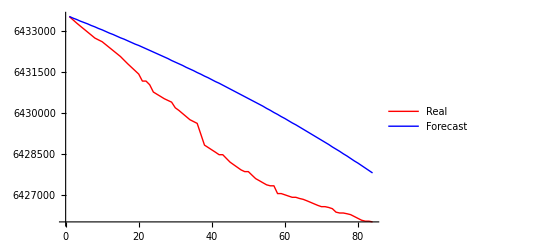

```mathematica
ListLinePlot[{Sdata,forecast},PlotStyle->{Red,Blue},PlotLegends->{"Real","Forecast"}]
```